```mathematica
f[x_] := 0; 
a := 0;
Φ[x_] = Limit [ ∑_(i=1)^n f[ a + i*(x-a)/n] *(x-a)/n, n->∞];
Plot [ {f[x], Φ[x]}, {x,0,3}]
```

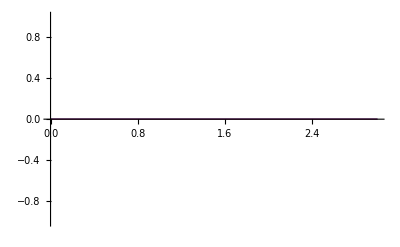

```mathematica
Talbe[ {x, Φ[x]}, {x,0,4}] //TableForm
```

Talbe[{x,0},{x,0,4}]

```mathematica
Integrate [1/(x^2 +1), {x, 1, 3}]
%// N
-π/4 + ArcTan [3]
```

-π/4+ArcTan[3]

0.463648

```mathematica
-π/4+ArcTan[3]
∫_0^π Sin[3x]Cos[2x]ⅆx
```

-π/4+ArcTan[3]

```mathematica
6/5

Assuming [ x>0, ∫_1^x 1/t^2ⅆt]
```

6/5

```mathematica
(-1+x)/x

FresnelS[1] // N
```

(-1+x)/x

0.438259

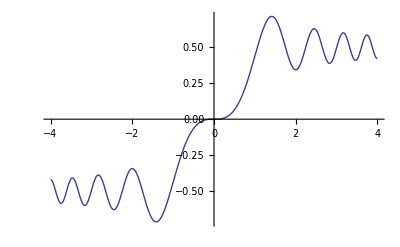

```mathematica
Plot[ FresnelS[x], {x, -4, 4} ]
```